```mathematica
Factor[-I*ω^3-5 ω^2+8*I*ω+4]
```

-ⅈ (-ⅈ+ω) (-2 ⅈ+ω)^2

```mathematica
Factor[v^3+5 v^2+8v+4]
```

(1+v) (2+v)^2

```mathematica
Expand[(1+I*ω) (2+I*ω)^2]
```

4+8 ⅈ ω-5 ω^2-ⅈ ω^3

```mathematica
Simplify[-1/(1+ⅈ ω)+3/(2+ⅈ ω)^2+1/(2+ⅈ ω)]
```

(ⅈ-2 ω)/((-ⅈ+ω) (-2 ⅈ+ω)^2)

```mathematica
ArrowsDeltaFunction[eqn_,x_]:=Module[{xsubs,listDeltas,coefDeltas,locationDeltas},xsubs=(x/.Cases[eqn,DiracDelta[a__]:>Solve[a==0,x],Infinity])/.x->{};
listDeltas=DiracDelta[x-x0]/.x0->xsubs;
coefDeltas=Flatten[Coefficient[eqn,listDeltas]];
locationDeltas=Flatten[xsubs];
Arrow[Table[{{locationDeltas[[i]],0},{locationDeltas[[i]],coefDeltas[[i]]}},{i,1,Length[locationDeltas]}]]]
```

```mathematica
f:=3*Pi*(∑_(n=-5)^5 DiracDelta[ω-Pi-3*n]+DiracDelta[ω+Pi-3*n])
```

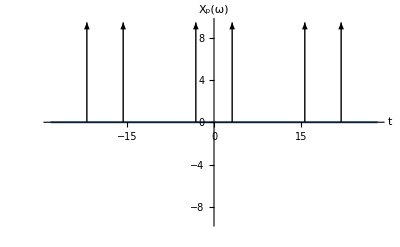

```mathematica
f:=3*Pi*(DiracDelta[ω-Pi]+DiracDelta[ω+Pi]+DiracDelta[ω-Pi-6*Pi]+DiracDelta[ω+Pi-6*Pi]+DiracDelta[ω-Pi-12*Pi]+DiracDelta[ω+Pi-12*Pi]+DiracDelta[ω-Pi+6*Pi]+DiracDelta[ω+Pi+6*Pi]+
DiracDelta[ω-Pi+12*Pi]+DiracDelta[ω+Pi+12*Pi])
Plot[f,{ω,-9*Pi,9*Pi},Epilog->{ArrowsDeltaFunction[f,ω]},AxesLabel->{t,"X_p(ω)"},PlotRange->3*Pi]
```

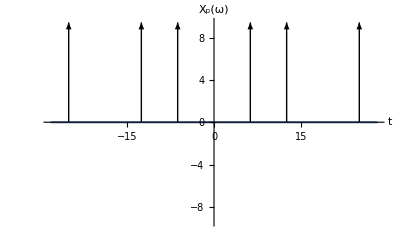

```mathematica
f:=3*Pi*(DiracDelta[ω-2*Pi]+DiracDelta[ω+2*Pi]+DiracDelta[ω-2*Pi-6*Pi]+DiracDelta[ω+2*Pi-6*Pi]+DiracDelta[ω-2*Pi-12*Pi]+DiracDelta[ω+2*Pi-12*Pi]+DiracDelta[ω-2*Pi+6*Pi]+DiracDelta[ω+2*Pi+6*Pi]+
DiracDelta[ω-2*Pi+12*Pi]+DiracDelta[ω+2*Pi+12*Pi])
Plot[f,{ω,-9*Pi,9*Pi},Epilog->{ArrowsDeltaFunction[f,ω]},AxesLabel->{t,"X_p(ω)"},PlotRange->3*Pi]
```

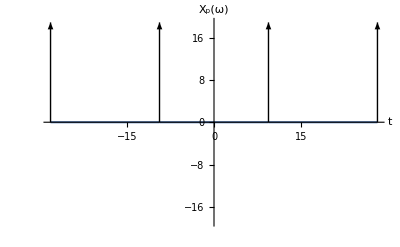

```mathematica
f:=3*Pi*(DiracDelta[ω-3*Pi]+DiracDelta[ω+3*Pi]+DiracDelta[ω-3*Pi-6*Pi]+DiracDelta[ω+3*Pi-6*Pi]+DiracDelta[ω-3*Pi-12*Pi]+DiracDelta[ω+3*Pi-12*Pi]+DiracDelta[ω-3*Pi+6*Pi]+DiracDelta[ω+3*Pi+6*Pi]+
DiracDelta[ω-3*Pi+12*Pi]+DiracDelta[ω+3*Pi+12*Pi])
Plot[f,{ω,-9*Pi,9*Pi},Epilog->{ArrowsDeltaFunction[f,ω]},AxesLabel->{t,"X_p(ω)"},PlotRange->6*Pi]
```

```mathematica
f:=3*Pi*(DiracDelta[ω-5*Pi]+DiracDelta[ω+5*Pi]+DiracDelta[ω-5*Pi-6*Pi]+DiracDelta[ω+5*Pi-6*Pi]+DiracDelta[ω-5*Pi-12*Pi]+DiracDelta[ω+5*Pi-12*Pi]+DiracDelta[ω-5*Pi+6*Pi]+DiracDelta[ω+5*Pi+6*Pi]+
DiracDelta[ω-5*Pi+12*Pi]+DiracDelta[ω+5*Pi+12*Pi])
Plot[f,{ω,-9*Pi,9*Pi},Epilog->{ArrowsDeltaFunction[f,ω]},AxesLabel->{t,"X_p(ω)"},PlotRange->3*Pi]
```

-Graphics-

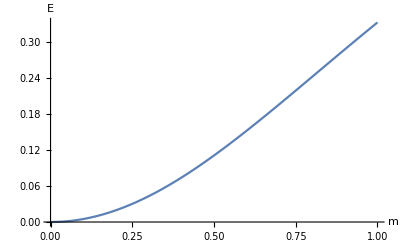

```mathematica
Plot[m^2/(m^2+2),{m,0,1},AxesLabel->{"m","E"}]
```